-Graphics3D-

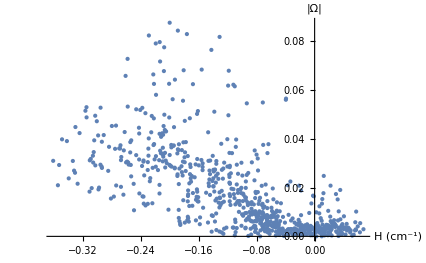

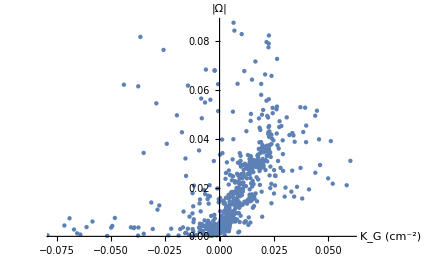

-Graphics3D-

Corr[|ė|, K_G] = -0.04050974897336711

Corr[|ė|, H] = -0.44973255062662329

Corr[|Ω̇|, K_G] = 0.19997868820442649

Corr[|Ω̇|, H] = -0.66975654720008198

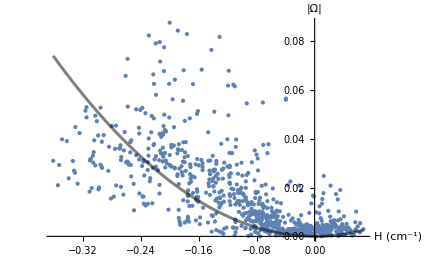

-Graphics3D-

Corr[|ė|, K_G] = -0.04050974897336711

Corr[|ė|, H] = -0.44973255062662329

Corr[|Ω̇|, K_G] = 0.19997868820442649

Corr[|Ω̇|, H] = -0.66975654720008198

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
defVerts = Import["verts_deformed.npy"];
initVerts = Import["init_verts.npy"];
verts = Import["verts.npy"];
simplices = Round[Import["tris.npy"]] + 1;
arealDefs = Sqrt[Import["areal_defs.npy"]//Flatten];
eccentricities = Sqrt[Import["eccentricities.npy"]//Flatten];
numTris = Dimensions[simplices][[1]];
numPoints = Dimensions[verts][[1]];
arealNormalizedDefs = arealDefs/Max[arealDefs];
eccNormalizedDefs = eccentricities/Max[eccentricities];
Tri[i_]:= {ColorData["TemperatureMap"][arealNormalizedDefs[[i]]],Triangle[verts[[simplices[[i]]]]]}
iTri[i_]:= {ColorData["TemperatureMap"][eccNormalizedDefs[[i]]],Triangle[verts[[simplices[[i]]]]]}
Tris = Tri /@ Range[numTris];
iTris = iTri /@ Range[numTris];
g1 = Graphics3D[{Tris}, Boxed->False]
g2 = Graphics3D[{iTris}, Boxed->False];



gaussCurvatures = Import["gauss_curv.npy"]//Flatten;
meanCurvatures = Import["mean_curv.npy"]//Flatten;
l1 = ListPlot[Transpose[{( meanCurvatures), arealDefs}],  AxesLabel->{"H (cm^-1)", "|Ω̇|"},AxesStyle->Directive[Bold,15,FontFamily->"Helvetica"], PlotStyle->{PointSize[0.007]}]
l2 = ListPlot[Transpose[{meanCurvatures, eccentricities}],  AxesLabel->{"H/cm^-1", "|ė|"},
AxesStyle->Directive[AbsoluteThickness[0.5],12,FontFamily->"Helvetica"]];
l3 = ListPlot[Transpose[{gaussCurvatures, arealDefs}],  AxesLabel->{"K_G (cm^-2)","|Ω̇|"},AxesStyle->Directive[Bold,15,FontFamily->"Helvetica"]]
l4 = ListPlot[Transpose[{gaussCurvatures, eccentricities}], AxesLabel->{"K_G", "|ė|"},AxesStyle->Directive[Bold,15,FontFamily->"Helvetica"]];

inds = Position[gaussCurvatures, x_/; x>0]//Flatten;
l5 = ListPointPlot3D[Transpose[{meanCurvatures[[inds]],gaussCurvatures[[inds]], arealNormalizedDefs[[inds]]}], AxesLabel->{"H","K_G", "|Ω̇|"},AxesStyle->Directive[AbsoluteThickness[0.5],12,FontFamily->"Helvetica"]]

l6 = ListPointPlot3D[Transpose[{meanCurvatures,gaussCurvatures, eccentricities}], AxesLabel->{"H","K_G", "|ė|"},AxesStyle->Directive[AbsoluteThickness[0.5],12,FontFamily->"Helvetica"]];

Print["Corr[|ė|, K_G] = " , Correlation[eccentricities, gaussCurvatures]]
Print["Corr[|ė|, H] = " ,Correlation[eccentricities, meanCurvatures]]
Print["Corr[|Ω̇|, K_G] = " ,Correlation[arealDefs, gaussCurvatures]]
Print["Corr[|Ω̇|, H] = " ,Correlation[arealDefs, meanCurvatures]]

data = Transpose[{meanCurvatures, arealDefs}];
ff= FindFit[data,((*a +  b x +*) c x^2),{(*a,b,*)c},x];
f1 = Plot[((*a +  b x +*) c x^2)/.ff, {x,Min[meanCurvatures],Max[meanCurvatures]},PlotStyle->{Black, Thickness[0.005], Opacity[0.5]},  AxesLabel->{"H", "(Ω̇)^2"},AxesStyle->Directive[AbsoluteThickness[0.5],12,FontFamily->"Helvetica"]];
f2 = Plot[(0.336-  0.336x + 0.336 x^2)^2, {x,-5,5},PlotStyle->Red,  AxesLabel->{"H", "(Ω̇)^2"},AxesStyle->Directive[AbsoluteThickness[0.5],12,FontFamily->"Helvetica"]];
Show[l1, f1]
```

```mathematica
BarLegend["Temperature"]
```

```mathematica
gaussCurvatures[[inds//Flatten]]
```

{0.00292473098566666673,0.0144891615233333337,-0.00236701852399999989,0.0119947818289999984,0.000796852398333333461,0.0201951434293333315,-0.00596564189900000014,-0.00441969067066666759,-0.00764699235066666674,0.022666501691333333,-0.00917246063999999951,0.00844898780000000009,-0.00356673420533333346,0.00987666031500000069,-0.00868467414899999797,-0.00056814866466666674,0.00437822774066666618,0.0209756131573333345,0.00415646716266666622,-0.154230269090333327,0.0255443054769999983,-0.0792103303366666761,0.00328978769500000044,-0.00386704762600000029,-0.127933065468333301,-0.00101020314000000019,-0.164468780570333317,-0.140369778387333333,0.00384195865466666585,-0.0669847525419999951,0.00241476657433333354,0.0149985146793333354,-0.120095215069333336,0.0343466524219999958,0.000129485928333333231,0.00409804933199999985,-0.000210881355333333371,0.0196297009129999985,0.0184197089883333352,-0.00666336995833333255,0.0144500090836666689,0.0142978784760000015,-0.00720896449233333295,-0.0165707174613333348,-0.0030622592473333334,-0.00511265779566666672,-0.00599044593566666703,-0.00455037712566666672,-0.00474760143866666696,0.0189953560886666657,-0.000411220432999999744,0.0048434526579999998,-0.00904847544699999978,0.00293384084266666697,-0.0121246784786666669,0.0209063192040000005,0.0118881147499999996,0.0340175302229999976,0.026482290226000002,0.00746493393900000014,0.0193698250450000005,0.0178331579846666664,0.0196945014623333345,0.0166896221780000013,0.0227793721890000023,-0.00845340280099999945,-0.00421859099599999985,0.0137986139150000006,0.0191769075843333352,-0.000680505174999999712,-0.0196283764103333362,-0.0126901479676666679,-0.0440336780979999967,-0.0395069955286666691,0.00615906238133333284,0.00644976780500000017,0.0188310046043333318,0.00116619153400000005,0.00454768158433333392,0.00555402219233333289,0.0145293682073333371,0.0075381148593333348,-0.00459242296533333375,0.00282990969433333283,0.00423710342966666671,0.00983938855233333458,0.0107771161396666686,0.00437611474166666684,0.0137013871956666658,0.00423225066033333392,0.0017861676316666662,0.00230399489266666646,0.00716607984299999935,0.00238011016366666654,0.00360096325766666664,0.00271690239466666631,0.013861611301999999,0.00491515119566666645,0.0240819247236666693,0.00714863967633333399,0.0239056899283333346,0.0225563602983333313,0.0139275281063333343,0.00674733926999999956,0.0216238714833333345,0.0263192431216666689,0.0212590969079999997,0.0170425490586666693,0.0247679372146666667,0.0158719919606666697,0.0239063099060000013,0.0142565687056666664,0.0290659666589999956,0.011467575201999999,0.0228012790353333376,0.0385248837956666673,0.00360641626833333286,0.00239264292366666654,0.0177600005726666656,0.0106628812156666659,0.00888756944566666644,0.0230166806329999973,0.0038773704306666666,0.00106260738099999991,0.00352503126233333353,0.0174155685263333339,0.0147039102659999987,0.00432890662066666692,-0.116048844486666677,0.00127976057700000031,0.006979117363333333,0.0126468160153333318,-0.104683746916000006,-0.0969734315423333299,0.00906430426366666535,0.0499944293029999931,0.0192292280999999989,0.0335078744416666685,-0.0920868282976666785,-0.11819863593933333,-0.0848548445100000132,-0.175493620699333358,-0.00806705782266666643,-0.117107823833999994,0.0411730413083333316,0.0440864886033333278,0.0173253118533333306,0.00898109242199999873,0.0440320228223333374,0.0193333318483333329,0.0180862465603333321,0.00622209723966666694,0.0226948498859999986,0.0144185124059999989,-0.00281921645599999974,0.00838344018066666634,-0.00535955261200000022,-0.00521071032933333438,-0.000864886028000000037,-0.00432564351800000021,-0.00148275458799999979,-0.00163167051633333307,-0.00225152774800000018,0.0011976509446666667,0.00287226103833333269,-0.00013974215800000001,-0.000815616788333333419,-0.145163143536999995,-0.0307460625376666658,-0.00883013647933333229,-0.037509852673999998,0.000452881800333333274,0.00937758786500000018,0.000834273067000000233,0.0372813569659999969,0.00164543188099999988,0.0284588926743333352,-0.0056252162936666671,-0.00406189259733333308,-0.00899760147766666581,0.0163419496086666637,-0.0154370691306666696,0.00634653140466666637,-0.00309899919799999993,0.00651872002666666756,-0.00845736316699999963,-0.000668337520666666542,0.00070038783766666684,0.0219556536600000012,0.00073566601466666659,-0.137873070788666646,0.0280691891470000003,0.00282389477600000207,0.00245469355166666675,-0.0408008585409999972,-0.161181668052333332,-0.000562254091999999837,-0.195230723472666679,-0.02857264991266667,-0.0862798356889999951,0.00601072627633333304,0.0089978459056666675,-0.100489333813333318,0.0250392231346666661,-0.00044095142600000006,0.00630760224766666738,0.000198324878333333332,0.0158489907009999979,0.0101264688493333324,-0.00225124713166666634,0.00426485906233333399,0.00875870357933333267,-0.00548289670566666585,-0.0180923283133333328,0.00429814228899999973,-0.00718079204199999904,-0.00729801913899999922,-0.00216702549233333333,-0.00344859555166666726,0.0100454744426666659,-0.00841136419033333346,-0.005908175825666666,-0.0140590013966666663,-0.00416577399066666698,-0.0154373258269999997,0.0229839418206666639,0.0109971731513333337,0.0345659407610000025,0.0244670689063333328,0.00455182006466666681,0.00870623095533333384,0.0187705707280000043,0.015268977630333332,0.0186627639696666653,0.0219393715676666663,-0.00264416371533333352,0.0013315511163333332,0.0116570795063333319,0.0123503055306666675,-0.00225103490333333333,-0.00818030449766666591,-0.0242919330173333309,-0.0290988348623333337,-0.0349358387633333309,0.00683069680133333371,0.00829229581099999967,0.0167828810913333328,-0.00668476011433333239,0.00294284040000000052,0.00227959528899999986,0.0104499881879999996,0.00553140895800000032,0.000316527577000000066,0.00634573358433333356,0.00633585373466666671,0.00730961278633333444,0.00980828942933333232,0.0074030724303333342,0.0150654195846666675,0.00407570513499999967,0.00332298938433333311,0.00381227345000000007,0.00576547398966666558,0.0022120147839999999,0.0051132408493333335,0.00348384226799999981,0.0103310152350000011,0.00408984189533333296,0.0223840327359999987,0.00475425235133333356,0.020216269964666668,0.0156763009893333347,0.0174845197906666645,0.00919794229800000203,0.0182127078126666647,0.0264178888509999967,0.00866084740666666665,0.0107052057650000015,0.0134766145146666683,0.00403162785399999949,0.0177531829653333334,0.011995652360999998,0.0234137955946666643,0.00915734014433333167,0.0186577650783333326,0.0291540661196666613,0.0065605604583333331,0.0040663909670000005,0.0161418396403333331,0.0046153315963333337,0.0125956533836666662,0.0165963329586666653,0.00326258501933333368,-0.0000697749010000000181,0.00312555826233333308,0.0165986710676666628,0.0156095557286666659,0.0035347735259999998,-0.100944095361000005,0.00394896054099999963,0.00613562001633333274,-0.0498749720193333371,-0.104855741135666661,-0.112034062220666655,0.013452102048999999,0.0602194181633333367,0.027473465629666665,0.0512111706353333349,-0.101247605139333327,-0.114373116743999984,-0.166913807146999993,-0.143320588632333323,-0.178227798457999992,-0.164102502473666673,-0.0655242925630000056,-0.152107307806999992,0.0380543231036666665,-0.027739529734000002,0.0196637357736666636,0.000976031974666666745,0.0372069683743333352,0.0147983032033333333,0.0303587546276666599,0.00461998901533333325,0.0138309662906666662,0.0128760758636666667,0.00144310718500000046,0.0130451035843333323,-0.00428470274166666693,-0.00360515895533333394,0.00480824982466666624,-0.003883368298,0.0010410156926666666,-0.00212814976933333377,-0.00314187968466666731,0.000410007427666666613,0.00244832173166666632,0.00125920950666666659,-0.00604901051100000062,-0.095867044744666674,-0.00837543403133333281,-0.0493700796466666689,-0.126321296597999982,0.00438511347766666702,0.0110094571236666657,-0.00300213285766666666,0.0255180813066666727,-0.000836515147999999866,0.0309272926930000032,-0.00362885887466666635,-0.00390963436100000023,-0.00679767854833333417,0.02253944015833333,-0.0117442176923333325,0.0142166996966666681,-0.00449007291300000059,0.0126420372209999996,-0.0120196569589999993,0.0035952524323333338,0.00265774737033333324,0.0226076374196666659,0.00920978430366666684,-0.125667276567333341,0.019373405611333331,-0.069042931061333343,0.00234886188599999976,-0.0236004040799999981,-0.121217478288999994,-0.0105306709013333333,-0.159709215744999994,-0.138819407123999983,0.0292598710553333315,-0.0392231863413333298,0.00434429736766666665,0.00947646578333333385,-0.109457392030666678,0.0250876370833333327,0.000271816755000000047,-0.000596750569333333357,-0.000938533471999999924,0.00761778367400000028,0.00717291766599999908,-0.0052676486880000005,0.00964595592433333503,0.00477825355433333324,-0.00228366024533333293,-0.0138200043136666659,0.000785743510666667036,0.00213950962033333325,-0.00385743239933333338,0.000180563765333333287,-0.00382178338366666705,0.018938334380666666,-0.00644104066666666749,0.00331853258100000062,-0.0113793062416666663,0.00185777078133333323,-0.00920776191999999986,0.0229145619456666665,0.0203771458843333315,0.0235525085816666625,0.0195398769230000005,0.00507128030533333333,0.0148914617030000002,0.021628931190333333,0.022326957109333332,0.0232823390570000011,0.0217982598439999988,-0.0156940388173333334,0.00273703531933333329,0.00925720774966666722,0.0191617689653333333,-0.0145310941676666666,-0.0257897939859999988,-0.00693621963633333366,-0.0364336997319999953,-0.0188780087116666683,0.014921286650666667,0.016495250210000003,0.022582366555333331,-0.000626021045666666672,0.00247626279433333339,0.0029496806776666668,0.0155548340260000025,0.0054393938313333336,0.000514767152666666485,0.00567338738166666811,0.00810899280233333408,0.00804791875366666666,0.00781925496966666585,0.00528197795799999897,0.0107621964960000014,0.00233160771733333322,0.00187298491933333348,0.0035102132886666664,0.00729184257166666777,0.00310664594799999957,0.00624018332433333347,0.00401780918300000036,0.0148230200680000007,0.00632053083466666693,0.0229639294553333345,0.00817619006033333366,0.022519585288000004,0.0177924529316666677,0.021758867009666668,0.0121701047910000026,0.0143490687936666667,0.0225002303483333339,0.0109819346413333324,0.0147561984739999989,0.0186071584383333301,0.00626842905166666645,0.0184376086719999985,0.0142751912630000016,0.0178011444133333342,0.00453594601633333389,0.017108376790000001,0.0398806538263333302,0.00602359435666666599,0.00262528894100000007,0.0103989583743333332,0.00721479176400000033,0.00807029733466666649,0.017256049097999996,0.00697998007666666628,0.00193162227233333321,0.00221433835733333322,0.00985005970366666789,0.0114103535663333325,0.00445665357533333358,-0.117107723090999996,-0.0120720953919999999,0.014184345445666666,0.00460874125333333301,-0.0890480744619999848,-0.112023896514999999,0.00624823536933333257,0.0521029565016666654,0.0334489305456666664,0.0462582163346666672,-0.0820224211573333251,-0.0999548117713333212,-0.148387542739666672,-0.185625305138999996,-0.105719545272000004,-0.158684101261666655,-0.0517070293313333304,-0.120747174430000007,0.023888325828666665,0.0330572474026666688,0.0266851841683333341,0.00472292234400000042,0.0393869916700000031,0.0272143756900000006,0.0217997352956666619,0.0138038879923333344,0.00901901555933333314,0.00753448745200000023,-0.00139679985566666643,0.00618623778333333291,-0.00442589232933333302,-0.00412471898766666664,0.00276583855733333363,-0.00541265574733333383,-0.00174450148533333328,0.000441346380666666658,-0.0033960008560000002,-0.000964915680333333289,0.000995689889666666632,0.00122787789299999995,-0.00312985260733333317,-0.150718692838000018,-0.0123782189673333331,-0.0584877726780000037,-0.0612044062943333314,0.00237053672000000007,0.0112907809233333337,-0.00197875875600000018,0.0238538561823333321,0.000268298184999999896,0.027623696901,-0.00530172838533333329,-0.00390924324133333414,-0.00815554109166666784,0.0215892251433333349,-0.0124276255956666665,0.00967613123566666601,-0.00363672532800000036,0.00917404336066666819,-0.00945795202099999899,0.000559645209666666623,0.00271134587633333314,0.0227185410909999976,0.00445396467466666664,-0.144842269416666669,0.0257525394163333303,-0.0481974691299999966,0.00266409708966666714,-0.0222581282060000003,-0.128195578257999987,-0.00321440152933333322,-0.176916925853000007,-0.155040860816666654,0.00767954709733333334,-0.0640648044683333334,0.0045850778476666668,0.0105740701790000002,-0.110854529160666668,0.029972410510000002,-0.00062015746666666666,0.00322242711199999992,-0.000432247659000000101,0.0153242419059999996,0.0121449548126666643,-0.0044297682553333332,0.00930919449833333447,0.00967045838266666728,-0.00500777590299999933,-0.0168135118933333307,0.00048226531133333363,-0.0037267659056666666,-0.00564872614033333411,-0.00242463022966666686,-0.00399704479566666705,0.0155931586896666669,-0.0059831480303333337,0.000249793348333333422,-0.0118610977566666661,-0.000362820078666666903,-0.0124631835720000004,0.0225768596416666689,0.0149730960106666672,0.0321759513653333343,0.0244310649480000003,0.00531487726333333341,0.0146854058666666676,0.0195347924323333345,0.0201767085830000005,0.0192458216156666667,0.0213970996320000002,-0.00941392315499999834,0.000202087684666666777,0.0110917312223333328,0.0181259508233333339,-0.00628731996499999959,-0.0173138718019999992,-0.0145719259719999991,-0.0374282360000000036,-0.0314036924619999977,0.0101932491663333322,0.0113862837293333338,0.0202373780809999987,-0.00225633952800000006,0.00324698800100000013,0.00338431490099999968,0.0130152659530000017,0.00605497242333333328,-0.00101366633600000005,0.00472634069833333375,0.0063294231810000004,0.00806475127233333318,0.00951212104299999951,0.00576251412099999891,0.0133902991656666675,0.00339212542933333338,0.00209396959299999958,0.00301426363200000018,0.00655768090466666686,0.00251871618266666635,0.00497955124566666629,0.00323270473366666635,0.0125780668380000016,0.00473604637366666689,0.0238653217779999961,0.00622856567133333369,0.0228085585100000036,0.0191047917220000009,0.0180673937216666684,0.00893073017400000148,0.0183539388826666657,0.0262188377883333344,0.0138728362516666679,0.0138468445400000001,0.019876356431666669,0.00848141405900000069,0.0200683906703333359,0.0132620523010000008,0.0232630370153333321,0.00761612402333333369,0.019183516205999996,0.0398179947076666638,0.005305381390333333,0.00295702704666666672,0.0147366685410000014,0.00689081561700000036,0.00967909335566666772,0.0185826743889999993,0.00416540295866666636,0.000854771305333333208,0.00369795232233333321,0.0142413142499999996,0.0131240950666666658,0.00491104294433333376,-0.112157483631000018,-0.00291381135099999999,0.00924022012799999987,-0.00903918957333333349,-0.104704031835000003,-0.103102993236333332,0.00862059208433333356,0.0585179234830000006,0.0269297683856666685,0.0457734629866666729,-0.0942422367536666639,-0.108423427988666665,-0.190044426747666639,-0.184402061551000002,-0.117624208259333341,-0.168774848984666659,-0.0373643091929999963,-0.137799205996000013,0.0356479020903333332,0.023339284823999995,0.0204064219646666635,0.0044656387530000001,0.0448314715779999998,0.0211536200990000006,0.0226966109279999988,0.00700167125200000084,0.0156667573823333316,0.0111721873026666679,-0.00118700823633333336,0.0084505288123333331,-0.00464831135400000078,-0.00433948531733333379,0.0014549392303333335,-0.00481964007800000059,-0.000982357443333333478,-0.00126080048433333328,-0.00314850880266666702,0.00016225891566666668,0.00242255147133333326,0.000668444552999999768,-0.00425416136466666688,-0.130478963398666686,-0.0158289512450000003,-0.034907670801999996,-0.0714189287083333291}

```mathematica
(*for time0*)
{arealDefs//Mean,
eccentricities//Mean,
arealDefs//Max,
eccentricities//Max}
{Correlation[eccentricities, gaussCurvatures],
Correlation[eccentricities, meanCurvatures],
Correlation[arealDefs, gaussCurvatures],
Correlation[arealDefs, meanCurvatures]}
```

{1.67793626521055202×10^-6,0.0000147724097549389195,0.000025200322260253936,0.000405776955315804652}

{-0.17837455859466967,0.10479413127957775,-0.16907497499324596,-0.00444636576534369}

```mathematica
(*for time5*)
{arealDefs//Mean,
eccentricities//Mean,
arealDefs//Max,
eccentricities//Max}
{Correlation[eccentricities, gaussCurvatures],
Correlation[eccentricities, meanCurvatures],
Correlation[arealDefs, gaussCurvatures],
Correlation[arealDefs, meanCurvatures]}
```

{7.9768168625999173×10^-7,7.92673943122016509×10^-6,0.0000132166996890779661,0.00013908090894550868}

{-0.55518730026917932,0.43430857725814229,-0.52298652801519541,0.20493100279938436}

```mathematica
(*for time8*)
{arealDefs//Mean,
eccentricities//Mean,
arealDefs//Max,
eccentricities//Max}
{Correlation[eccentricities, gaussCurvatures],
Correlation[eccentricities, meanCurvatures],
Correlation[arealDefs, gaussCurvatures],
Correlation[arealDefs, meanCurvatures]}
```

{7.69476958392708843×10^-7,5.83860219656264478×10^-6,0.0000153228823744547424,0.000112312992661625375}

{-0.22079173253025829,0.06633696122013475,-0.0162997792658693,-0.06946287399521831}

```mathematica
(*for time12*)
{arealDefs//Mean,
eccentricities//Mean,
arealDefs//Max,
eccentricities//Max}
{Correlation[eccentricities, gaussCurvatures],
Correlation[eccentricities, meanCurvatures],
Correlation[arealDefs, gaussCurvatures],
Correlation[arealDefs, meanCurvatures]}
```

{0.0000725483926210846674,0.000861873910238764061,0.00274633628102586387,0.0281279468980903218}

{0.23560656486946896,0.53526216160260676,0.43751399001763031,0.60928621731193106}

```mathematica
Show[g1]
Show[g2]
```

-Graphics3D-

-Graphics3D-

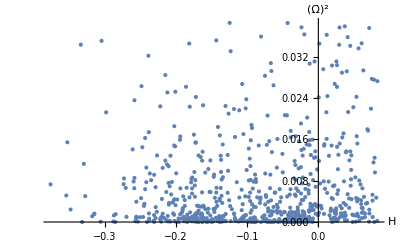

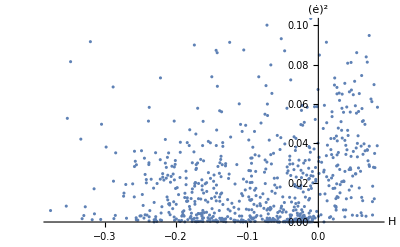

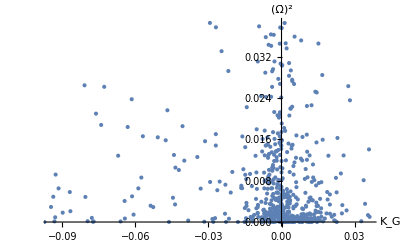

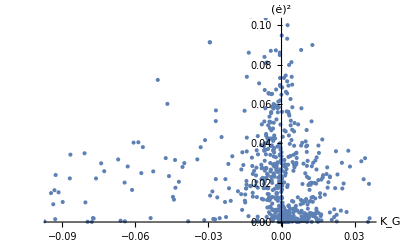

```mathematica
l1
l2
l3
l4
```

```mathematica
Correlation[eccentricities, gaussCurvatures]
Correlation[eccentricities, meanCurvatures]
Correlation[arealDefs, gaussCurvatures]
Correlation[arealDefs, meanCurvatures]
```

-0.8112788523246625

-0.42887695107676808

-0.69506806001705779

-0.36771435087829428

```mathematica
(*tangentX = Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\tangent_x.npy"];
tangentY = Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\tangent_y.npy"];
tangentZ = Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\normals.npy"];*)
initVerts = Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\init_verts.npy"];
tangentField = Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\tangent_field.npy"];
normals = Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\unit_normals.npy"];
faces = Round[Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\faces.npy"]]+1;
ϵ = 0.075;
(*arrowX[i_]:= {initVerts[[i]], initVerts[[i]] + ϵ tangentX[[i]]}
arrowY[i_]:= {initVerts[[i]], initVerts[[i]] + ϵ tangentY[[i]]}
arrowZ[i_]:= {initVerts[[i]], initVerts[[i]] + ϵ tangentZ[[i]]}
arrowsX = arrowX /@ Range[numPoints];
arrowsY= arrowY /@ Range[numPoints];
arrowsZ= arrowZ /@ Range[numPoints];*)
numVerts = Dimensions[initVerts][[1]]
numTris = Dimensions[faces][[1]]
arrowT[i_]:= {initVerts[[i]], initVerts[[i]] + ϵ tangentField[[i]]}
arrowsT= arrowT /@ Range[numVerts];
arrowN[i_]:= {initVerts[[i]], initVerts[[i]] + ϵ normals[[i]]}
arrowsN= arrowN /@ Range[numVerts];
gTri[i_]:= {Triangle[initVerts[[faces[[i]]]]]}
gTris = gTri /@ Range[numTris];
g1 = Graphics3D[{gTris,Arrowheads[0.01],Green, Arrow[arrowsT](*,Blue, Arrow[arrowsN]*)}, Boxed->False]
```

10100

20000

-Graphics3D-

```mathematica
initVerts//Dimensions
```

{766,3}

```mathematica
initVerts[[1]]
```

{0.542192000000000007,-0.944822999999999968,-0.0754650000000000043}

```mathematica
max= 1 Max[gaussCurvatures];
Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\verts_deformed.npy"];
initVerts = Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\init_verts.npy"];
gaussCurvatures = Import["C:\\Users\\Salem\\Dropbox (Harvard University)\\Mosleh-Mahadevan\\Morphometry\\Code\\gauss_curv.npy"]//Flatten;
normalizedGauss = gaussCurvatures/max;
Tri[i_]:= {Triangle[verts[[simplices[[i]]]]]}
defTri[i_]:= {Triangle[defVerts[[simplices[[i]]]]]}
Tris = Tri /@ Range[numTris];
defTris = defTri /@ Range[numTris];
g1 = Graphics3D[{Opacity[0.2],Tris}, Boxed->False];
g2 = Graphics3D[{defTris}, Boxed->False];
Show[g1, g2]
g1 = Graphics3D[{Tris}, Boxed->False];
g2 = Graphics3D[{Opacity[0.2],defTris}, Boxed->False];
Show[g1, g2]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*David results. loss of correlations after the registration algorithm*)
```

```mathematica
Show[g1]
Show[g2]
```

-Graphics3D-

-Graphics3D-

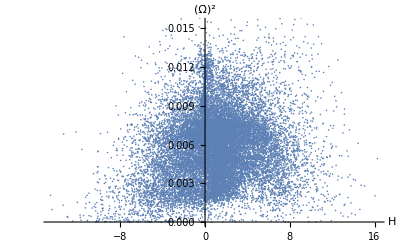

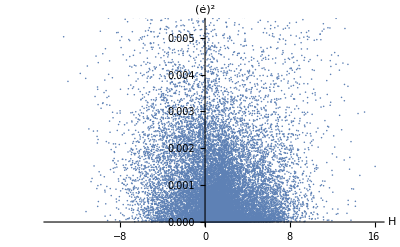

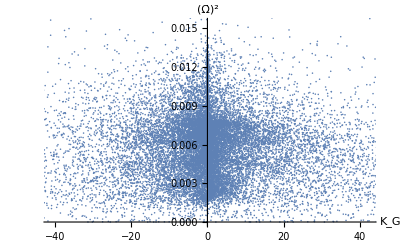

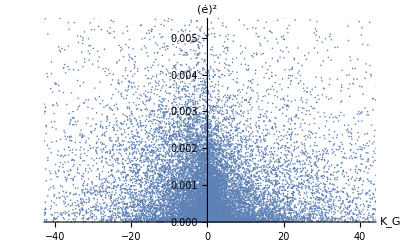

```mathematica
l1
l2
l3
l4
```

```mathematica
Correlation[eccentricities, gaussCurvatures]
Correlation[eccentricities, meanCurvatures]
Correlation[arealDefs, gaussCurvatures]
Correlation[arealDefs, meanCurvatures]
```

-0.00218284466275722

-0.06200492580125469

-0.102320940759061

0.1400480555467305

```mathematica
SetDirectory[NotebookDirectory[]];
theta1 =Import["theta_1.npy"];
theta2 =Import["theta_2.npy"];
phi1 =Import["phi_1.npy"];
phi2 =Import["phi_2.npy"];
X1 = Cos[phi1] Sin[theta1]//Flatten;Y1 = Sin[phi1] Sin[theta1]//Flatten;Z1 = Cos[theta1]//Flatten;
X2 = Cos[phi2] Sin[theta2]//Flatten;Y2= Sin[phi2] Sin[theta2]//Flatten;Z2 = Cos[theta2]//Flatten;
initPoints = Transpose[{X1, Y1, Z1}];
defPoints = Transpose[{X2, Y2, Z2}];
arrow[i_]:= Arrow[{initPoints[[i]], defPoints[[i]]}]
arrows = arrow /@ Range[Length[X1]];
arrowP = Graphics3D[{arrows}];
initP = ListPointPlot3D[Transpose[{X1, Y1, Z1}], BoxRatios->{1, 1, 1}, PlotStyle->{PointSize[0.02],Blue}];
defP = ListPointPlot3D[Transpose[{X2, Y2, Z2}], BoxRatios->{1, 1, 1},PlotStyle->{PointSize[0.02],Red}];
Show[arrowP, initP, defP]
```

-Graphics3D-

```mathematica
initP
defP
```

-Graphics3D-

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/QuantileRegression.m"]
```

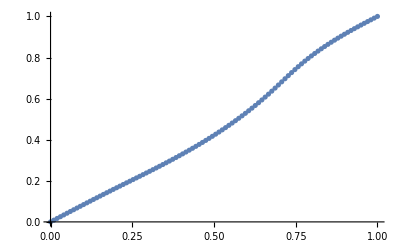

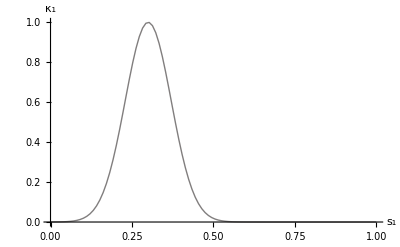

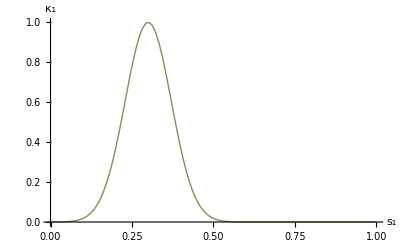

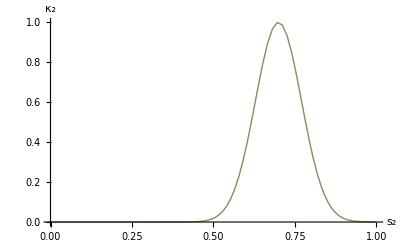

```mathematica
initCoords =Import["init_coordinates.npy"]//Flatten;
finalCoords =Import["final_coordinates.npy"]//Flatten;
initCurvatures =Import["init_curvatures.npy"]//Flatten;
finalCurvatures=Import["final_curvatures.npy"]//Flatten;

numberOfPoints = initCoords//Length;

registrationData = {initCoords, finalCoords}//Transpose;
initCurvatureData = {initCoords, initCurvatures}//Transpose;
finalCurvatureData = {finalCoords, finalCurvatures}//Transpose;


pr =ListPlot[registrationData, PlotRange->All, AxesLabel-> {"s_1", "s_2"}];
qfunc=QuantileRegression[registrationData,10,{0.5}][[1]];
pq = Plot[qfunc[x], {x,0,1}];
Show[pq, pr]

pκi1  = ListPlot[initCurvatureData, PlotRange->All, AxesLabel-> {"s_1", "κ_1"},Joined->True, ColorFunction->Function[{x, y}, Hue[x]], PlotStyle->Thick]
pκi2 = ListPlot[initCurvatureData, PlotRange->All, AxesLabel-> {"s_1", "κ_1"},Joined->True, ColorFunction->Function[{x, y}, Hue[qfunc[x]]], PlotStyle->Thick]
pκf = ListPlot[finalCurvatureData, PlotRange->All, AxesLabel-> {"s_2", "κ_2"},Joined->True, ColorFunction->Function[{x, y}, Hue[x]], PlotStyle->Thick]
```

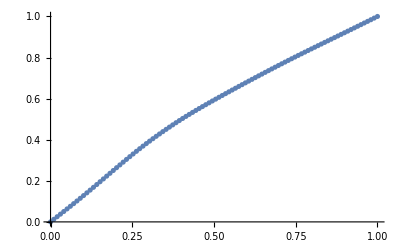

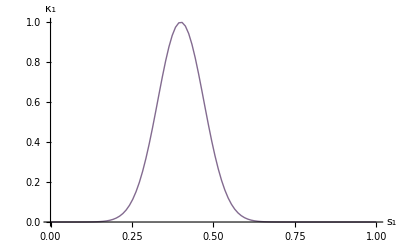

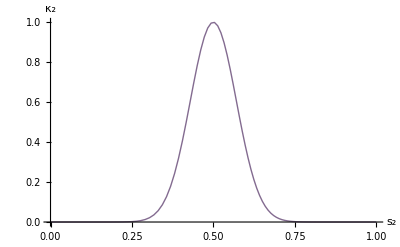

```mathematica
(*For peaks close to each other and points repelling each other, A = 1, B = 500, D & E = 1, G = 0.00001*)
```

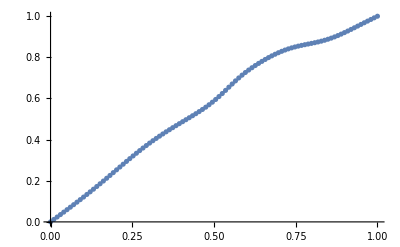

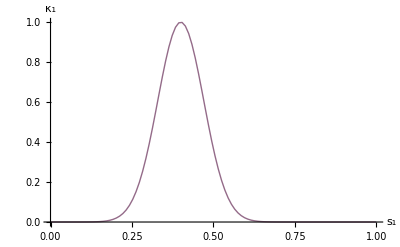

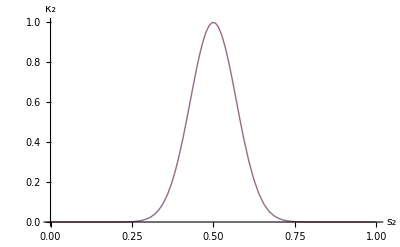

```mathematica
(*For peaks close to each other and points NOT repelling each other, A = 1, B = 500, D & E = 1, G = 0.
Only difference from the previous plots is that G = 0*)
```

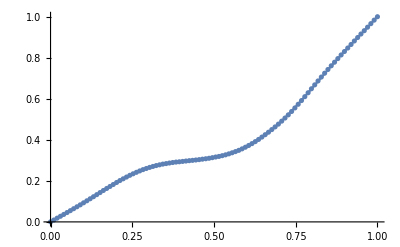

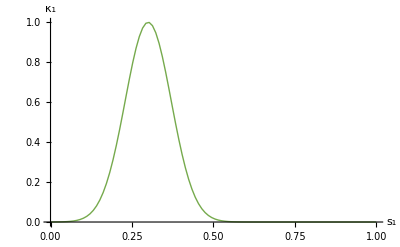

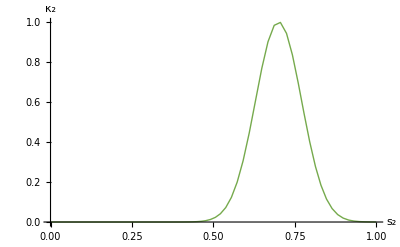

```mathematica
(*For peaks NOT close to each other and points NOT repelling each other, A = 1, B = 500, D & E = 1, G = 0.
Only difference from the previous plots is the position of the peaks. Notice that registration might not come out monotonic which is a problem.*)
```

```mathematica
(*For peaks NOT close to each other and points repelling each other, A = 1, B = 500, D & E = 1, G = 0.00001.
Same as previous plot but adding weak repulsion between points since G ≠ 0. 
When the points are farther apart things are not shifted to match the peaks.*)
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[] <> "Mesh_Data" <> "leaves"];
defVerts = Import["vertices_1.txt"];
initVerts = Import["vertices_0.npy"];
```

SetDirectory::cdir: Cannot set current directory to D:\Salem\Dropbox (Harvard University)\Morphometry\Code\Mesh_Dataleaves.

Import::nffil: File not found during Import.